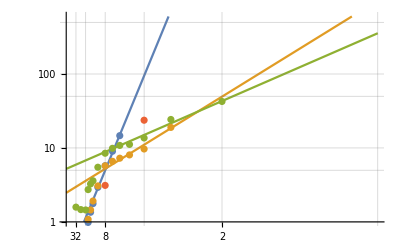

```mathematica
n=2^Range[5,0,-1];
size0={1024,1536,2048,2304,2560,2816,3328,4096,4864,5632};
time0={4,17,43,59,81,106,176,345,541,880}/60;
size1={1024,1536,2048,2304,2560,2816,3328,4096,4864,5632,6656,8192,11008};
time1={4,6,9,65,87,115,184,344,396,436,483,581,1138}/60;
size2={1024,1536,2048,2304,2560,2816,3328,4096,4864,5632,6656,8192,11008,16384};
time2={95,88,87,164,196,216,329,509,593,649,670,819,1456,2551}/60;
size3={4096,8192};
time3={187,1423}/60;
data0=Transpose[{size0,time0}];
data1=Transpose[{size1,time1}];
data2=Transpose[{size2,time2}];
data3=Transpose[{size3,time3}];
f0=NonlinearModelFit[data0,a Exp[-b x/1000],{a,b},x];
f1=NonlinearModelFit[data1[[8;;]],a Exp[-b x/1000],{a,b},x];
f2=NonlinearModelFit[data2[[8;;]],a Exp[-b x/1000],{a,b},x];
Show[
LogPlot[{f0[x],f1[x],f2[x]},{x,1,2^15}
,PlotRange->{All,{1,600}}
,Ticks->{Transpose[{(256Length[Range[128][[;;;;#]]])&/@n,n}],Automatic}
,GridLines->Automatic
,ImageSize->Full
]
,ListLogPlot[{data0,data1,data2,data3}]
]
```

```mathematica
phi=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\isinglass_05\\inputs\\fields\\20170302_28400.000000.h5","/Vmaxx1it"];
Q=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\isinglass_05\\inputs\\particles\\20170302_28400.000000.h5","/Qp"];
E0=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\isinglass_05\\inputs\\particles\\20170302_28400.000000.h5","/E0p"];
```

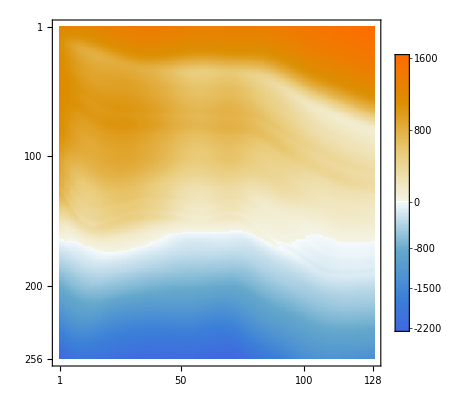

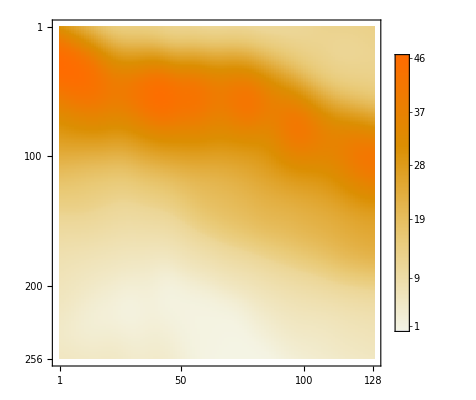

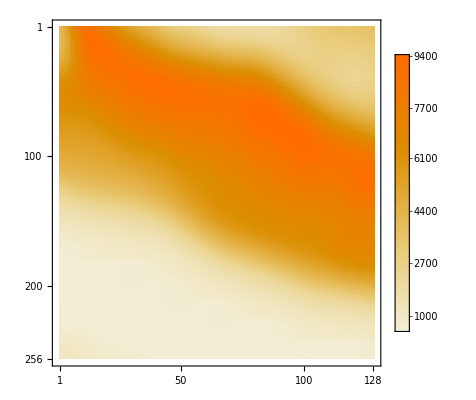

```mathematica
MatrixPlot[phi,AspectRatio->1,PlotLegends->Automatic]
MatrixPlot[Q,AspectRatio->1,PlotLegends->Automatic]
MatrixPlot[E0,AspectRatio->1,PlotLegends->Automatic]
```